```mathematica
Fórmula de Bethe-Bloch
```

NOTAS

Para ver más desglose teórico ver las nota de oneNote del cuaderno.

Contiene lo mismo cálculo de Bethe-Bloch que el cuaderno de Python, pero solo la forma simple. Y revisar el otro programa de C++ y ROOT, que calcula Bethe, diferentes materiales pero en función de la energía.

El fin, es entender como escribir toda la  forma de Bethe-Bloch en términos de una función de  𝒻(β · γ) con unidades de momento [MeV/c].

## Bethe-Bloch, para muon en Silicio; Forma de cociente I^2(1-β^2); sin correciones densidad

Para el elemento de Silicio y la partícula incidente un muon.

```mathematica
(*Constantes*)
z=1;                      (*carga partícula entrante µ^+*)
e=1.602*10^-19;(*carga del e⁻[Coulomb]*)
me=9.109*10^-31;(*masa del e⁻[Kg]*)
Na=6.022*10^23;(*num. Avogadro [1/mol]*)
Ne=Z*ρ*Na/A; (*densidad de e⁻, para material*)
Z=14;                    (*num. atómico Si*)
ρ=2330;                (*densidad Si [Kg/m.b3] *)
A=28*10^-3;       (*masa atómica Si [Kg/mol] *)
ϵ0=8.854*10^-12; (* permitividad vacío [F/m] *)
II=2.77*10^-17; (*potencial de excitación medio [Joules]*)
M=200*me; (*masa del µ~200·Subscript[m, e]*)
c=3*10^8;  (* vel. luz [m/s]*)
```

```mathematica
(*Funciones*)
```

En caso de quere escribir el programa en otro lenguaje, se deben escribir las funciones en términos de beta y gamma. Como  𝒻 → 𝒻 (β · γ).

```mathematica
γ[β_]:=1/(√(1-β^2));
βγ[β_]:=β*γ[β];
```

```mathematica
Tmax[β_]:=(2*me*c^2*(βγ[β])^2)/(1+(2*γ[β]*me)/M+(me/M)^2);
```

```mathematica
dEdx[β_]:=((2π*Ne*z^2*e^4)/(me*c^2*β^2*(4π*ϵ0)^2))*Log[ⅇ,(2*me*β^2*c^2*Tmax[β])/(II^2(1-β^2))]*0.01(*convert to cm*)*6.24*10^12(*convert to MeV*)
```

### Creación de puntos X Y, graficar

```mathematica
(*linspace de BETAS *) βs= Array[#&,100,{0.2,0.99999999}];
(*puntos X: β·γ*)
BG=βγ[βs];
(*puntos Y: dE/dx *)
DeDx=Table[dEdx[betas],{betas,βs}];(* dE/dx, es de los vals de β's*)
```

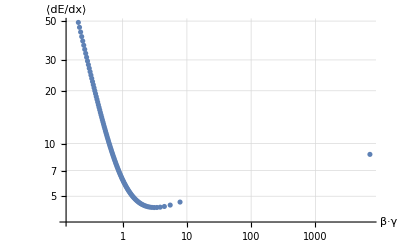

```mathematica
ListLogLogPlot[Transpose[{BG,DeDx}],AxesLabel->{Style["β·γ",Bold,17],Style["⟨dE/dx⟩",Bold,17]},GridLines->Automatic,PlotRange->All,PlotLegends->"Classical"]
```